# ALife 2023: Dynamics of Developmental Lineages

Gabriel J. Severino

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

DynamicalSystem::shdw: Symbol DynamicalSystem appears in multiple contexts {Dynamica`,Global`}; definitions in context Dynamica` may shadow or be shadowed by other definitions.

DisplayFlow::shdw: Symbol DisplayFlow appears in multiple contexts {Dynamica`,Global`}; definitions in context Dynamica` may shadow or be shadowed by other definitions.

## Defining System: 2 stage Topology #2

-Graphics-

```mathematica
topo1=DynamicalSystem[{L * STEM * (1-(STEM/k)) - P * 2 * L * STEM * (1-(DIFF/k)),P * 2 * L * STEM * (1-(DIFF/k))- d * DIFF},{{STEM,0, 10},{DIFF,0,10}}, {{L, -1, 1},{k, -10, 10}, {P, -1, 1}, {d,-1,1} }];
```

```mathematica
topo1a= topo1/.{L ->0.5 , k-> 5, P -> .5 , d -> 0.1};
```

## Defining System: 2 stage Topology #1

```mathematica
topo2=DynamicalSystem[{L * STEM * (1-(DIFF/k)) - (P * 2 * L * STEM * (STEM/k)),(P * 2 * L * STEM * (STEM/k))- d * DIFF},{{STEM,0, 10},{DIFF,0,10}}, {{L, -1, 1},{k, -10, 10}, {P, -1, 1}, {d,-1,1} }];
```

```mathematica
topo2a =topo2/.{L -> .5, k-> 5, P -> .5 , d -> 0.1};
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 209.405 and t = 238.336.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 219.85 and t = 250.835.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 224.267 and t = 255.704.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

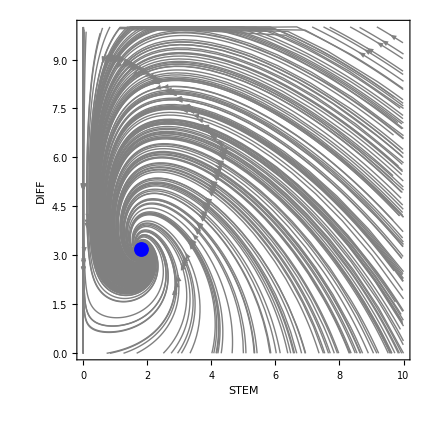

```mathematica
Show[DisplayFlow[topo2a , 1000, PlotStyle -> {Gray, Thin}], DisplayPhasePortrait[topo2a,SaddleManifolds -> True]]
```

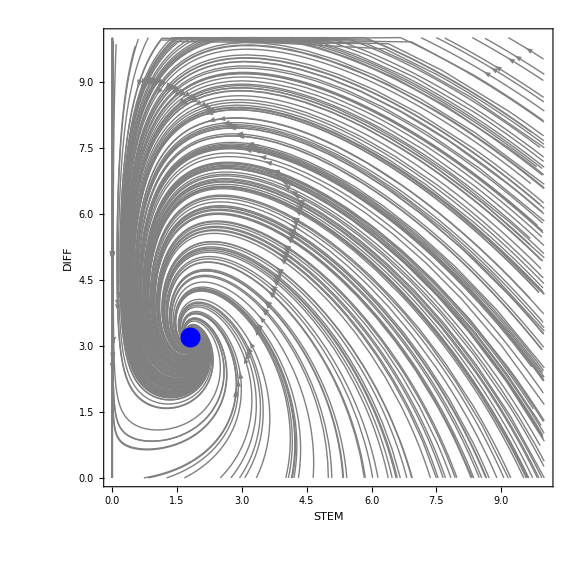

```mathematica
Show[%22,ImageSize->Large]
```

## Defining System: 3 stage Topology #2

```mathematica
Topo32 = DynamicalSystem[{LS*STEM*(1-STEM/k)-PS*2*LS*STEM*(1-INTER/k),PS*2*LS*STEM*(1-INTER/5)+LI*INTER*1-PI*2*LI*INTER*(1-DIFF/k),PI*2*LI*INTER*(1-DIFF/k)-DEATH*DIFF*1},{{STEM,0,50},{INTER,0,50},{DIFF,0,50}},{{LS, 0,10},{k,0,50},{PS, 0,1},{LI, 0,10},{PI, 0,1},{DEATH, 0,10}}];
```

```mathematica
Topo3b = Topo32/. {LS -> 0.5,k->5, PS -> .5, LI -> .5, PI -> .5, DEATH -> .1};
```

```mathematica
farfromeq = Topo32 /. {LS-> .5,k->33,PS-> 0.6,LI->.65,PI->.7,DEATH -> .3};
```

## Higher valued rates and probabilities:

Exploring bifurcations for a higher average system.

```mathematica
DisplayBifurcationDiagram[farfromeq ,PS,StateVariables->{STEM,INTER}]
```

-Graphics3D-

Identifying Limit cycles for the two Hopf Bifurcations.

```mathematica
$BifurcationDiagramBPs;
```

```mathematica
hopf1a = farfromeq /. {DEATH->0.3,k->33,LI->0.65,LS->0.5,PI->0.7,PS->1.5};
```

```mathematica
DisplayTrajectories[hopf1a,{{20,20,20}},10000]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1146.46.

-Graphics3D-

```mathematica
DisplayTrajectories[hopf1a,{{0.1785189573505495,26.94566701816578,21.55333066245206}},13]
```

-Graphics3D-

```mathematica
LC1234 = FindLimitCycle[hopf1a, First[Last[$Trajectories]],13]
```

LimitCycle[Stable,13.2218,{0.178519,26.9457,21.5533}]

```mathematica
LCB1234 = FollowLimitCycleBranch[LC1234, PS,MaxStepSize -> 0.001];
```

```mathematica
DisplayBifurcationDiagram[farfromeq ,PS,StateVariables->{STEM,INTER}, LimitCycleBranches->{LCB1234[[Range[1,Length[LCB1234],10]]]},AxesLabel -> {"PS","Stem cells", "Transit-Amplifying cells"}]
```

Warning: MaxSteps exceeded, terminating branch

Warning: A convergence failure occurred during continuation

Warning: MaxSteps exceeded, terminating branch

Warning: MaxSteps exceeded, terminating branch

-Graphics3D-

-Graphics3D-

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Fold,{-2.16645326485688,3.69462227928593,8.36590393361675},{DEATH→0.3,k→33,LI→0.65,LS→-0.159513752239625,PI→0.7,PS→0.6}],BifurcationPoint[Hopf,{-2.68740320373195,3.26049733022337,7.60956981329705},{DEATH→0.3,k→33,LI→0.65,LS→-0.145772369826759,PI→0.7,PS→0.6}],BifurcationPoint[Branch,{-6.59999999999999,0,0},{DEATH→0.3,k→33,LI→0.65,LS→0,PI→0.7,PS→0.6}],BifurcationPoint[Branch,{-1.37802197802197,4.35164835164835,9.42857142857143},{DEATH→0.3,k→33,LI→0.65,LS→0,PI→0.7,PS→0.6}],BifurcationPoint[Branch,{0,4.35164835164835,9.42857142857143},{DEATH→0.3,k→33,LI→0.65,LS→0,PI→0.7,PS→0.6}],BifurcationPoint[Hopf,{7.50730885415122,11.7560907117927,17.1392695814204},{DEATH→0.3,k→33,LI→0.65,LS→0.20534923353161,PI→0.7,PS→0.6}]}

Finding limit cycle for Hopf

```mathematica
hopfo = farfromeq/.{DEATH->0.3,k->33,LI->0.65,LS->0.20,PI->0.7,PS->0.6};
```

```mathematica
DisplayTrajectories[hopfo /. {LS -> 0.15},{{9.391205720448783,13.561767579825363,18.633224941317447}},10000]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 4273.4.

-Graphics3D-

```mathematica
Last[$Trajectories]
```

{{9.39121,13.5618,18.6332},{9.40453,13.8948,18.5571},{9.42794,14.1999,18.5742},{9.46062,14.4942,18.647},{9.50222,14.7874,18.7537},5352,{7.83179,8.0355,13.8456},{7.7129,8.129,13.9154},{7.60163,8.23294,13.9946},{7.49781,8.34796,14.0832},{7.40136,8.47485,14.1815}}
 |  |  |  |

```mathematica
DisplayTrajectories[hopfo,{{7.401356802414768,8.47485148173115,14.181474617437091}},55]
```

-Graphics3D-

```mathematica
LCLS = FindLimitCycle[hopfo,First[Last[$Trajectories]],55]
```

LimitCycle[Stable,58.3007,{7.78206,9.94323,15.9041}]

```mathematica
LCBLS = FollowLimitCycleBranch[LCLS, LS,MaxStepSize -> 0.001];
```

```mathematica
Show[DisplayTrajectories[hopfo,{{20,20,20},{20,20,0},{40,40,40},{0,0,0},{0,0,40},{40,0,0},{40,0,40},{40,40,0}},1000,PlotStyle -> {Gray,Thin},Arrows -> False,AxesLabel -> {"Stem cells", "Transit-Amplifying cells", "Differentiated Cells"}],DisplayPhasePortrait[hopfo,SaddleManifolds -> True, LimitSets -> {LCLS},SaddleManifoldStyle-> {Thickness[0.003]},Tries -> 100000]]
```

-Graphics3D-

```mathematica
DisplayBifurcationDiagram[farfromeq,LS,StateVariables-> {STEM,DIFF},LimitCycleBranches->{LCBLS[[Range[1,Length[LCBLS],3]]]},AxesLabel -> {"LS", "Stem cells", "Differentiated Cells"},PlotRange -> {{0.1,0.5},{0,40},{-10,40}}]
```

-Graphics3D-

## Defining System: 3 stage Topology #1

```mathematica
Topo31 = DynamicalSystem[{LS*STEM*(1-STEM/k)-PS*2*LS*STEM*(1-INTER/k),PS*2*LS*STEM*(1-INTER/k)+LI*INTER*(1-DIFF/k)-PI*2*LI*INTER*1,PI*2*LI*INTER*1-DEATH*DIFF*1},{{STEM,0,50},{INTER,0,50},{DIFF,0,50}},{{LS, 0,10},{k,0,40},{PS,0,1},{LI, 0,10},{PI, 0,10},{DEATH, 0,1}}]
```

DynamicalSystem[«3 ODEs»,{STEM,INTER,DIFF},{LS,k,PS,LI,PI,DEATH}]

```mathematica
Topo3a = Topo31/. {LS -> .185, k -> 15,PS -> .395, LI -> .35, PI -> .14, DEATH -> .04}
```

DynamicalSystem[«3 ODEs»,{STEM,INTER,DIFF},{DEATH→0.04,k→15,LI→0.35,LS→0.185,PI→0.14,PS→0.395}]

## Defining System: 3 stage # 10

Topology # 10

```mathematica
Topo31 = DynamicalSystem[{LS*STEM*(1-DIFF/k)-PS*2*LS*STEM*(STEM/k),PS*2*LS*STEM*(STEM/k)+LI*INTER*(INTER/k)-PI*2*LI*INTER*1,PI*2*LI*INTER*1-DEATH*DIFF*1},{{STEM,0,50},{INTER,0,50},{DIFF,0,50}},{{LS, 0,10},{k,0,40},{PS, 0,1},{LI, 0,10},{PI,0,1},{DEATH, 0,10}}]
```

DynamicalSystem[«3 ODEs»,{STEM,INTER,DIFF},{LS,k,PS,LI,PI,DEATH}]

```mathematica
Topo3a = Topo31/. {LS -> .185, k -> 15,PS -> .395, LI -> .35, PI -> .14, DEATH -> .04}
```

DynamicalSystem[«3 ODEs»,{STEM,INTER,DIFF},{DEATH→0.04,k→15,LI→0.35,LS→0.185,PI→0.14,PS→0.395}]